# Computing for Mathematical Physics

## Exercises 1: An Introduction to Computer Algebra

```mathematica
Clear["Global`*"]
```

Click on the line above and press ⇧+⌤.

When Mathematica has finished executing the command, for this command you will not see its reply printed in plain Courier on a line introduced by, Out[n]:= , but for most subsequent commands you will. Exceptions include other Clear commands, commands such as ?? to ask for information about a symbol or a function, and commands which have been terminated with a semicolon.

You can move up and down the notebook document by using the scroll bar on the right-hand side of the window.  When Mathematica is working on a cell, or group of cells, the associated cell-group brackets on the right-hand side will appear thicker than prior to triggering their evaluation with  ⇧+⌤. When their evaluation is complete, the right-hand cell-group brackets revert to thin grey lines.

You are encouraged to use Mathematica's built-in help in the course of these exercises.

## Handy Keyboard Shortcuts

At least for this first class you are free to input expressions in whichever way you find most convenient. 

Also, no text cells are needed in order to answer the questions for this first class. So you do not need to know how to change the format type of a Mathematica cell yet: the default input cell type is all you need today.

In the longer term, most people find it more efficient to learn at least a few very useful keyboard short-cuts, to avoid having to use the mouse. In this first class you might already find the short-cuts for superscript, square-root, pi, ⅇ, and infinity useful (next subsection).

However, with this being our first class, you are perfectly welcome to skip reading this section and move on to the questions: the section contains no questions.

### Frequently used mathematical notation

To use the palette and mouse to enter things like superscripts, integrals, etc, go to the drop-down menu at the top of the screen and select Palettes → Basic Math Assistant .

While it's fine to use the palettes to help enter expressions, particularly on meeting Mathematica for the first time, many people find it more useful and faster in the long-run to be able to enter everything from the keyboard, without any need to go to the mouse.

Some frequently used quick keyboard formulations are shown in the grey box below.
These are generally quite intuitive, and require only a very small investment of time to become fluent in; this pays dividends.

-Graphics-

[Copied from https://reference.wolfram.com/language/tutorial/MathematicalAndOtherNotation.html .]

### Switching from input cells to other cell format types, e.g. text cells

Changing the style of a cell (Input/Text) can be done via the drop-down menu at the top of the screen: Format → Style → Input/Text.

Note that Mathematica only interprets the contents of input cells as code to be processed and run. The contents of text cells is not interpreted as code by Mathematica, and is therefore left as-is. (Aside: one should be careful therefore, when entering code, to be clear that the cell you are working with is indeed an input cell and not a text cell. If in doubt, clicking Format → Style and looking for the ✓ will reveal the currently selected cell’s format type.)

By default all new cells are input cells. However, writing text cells is essential for communicating the purpose and meaning of code appearing in the input cells to the reader.

Alternatively, the next grey box below shows handy short-key entries for quickly changing the cell style format directly from the keyboard, avoiding the mouse: Alt+7 is especially useful, as it enables us to write text cells like this one, which one will do somewhat frequently later in this course.

Note, on a Mac, you would need to swap the Alt buttons below for ⌘.

-Graphics-

These and further keyboard shortcuts can be found here https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html .

### Greek letters

Entering Greek letters couldn’t really be more easy.
Typically, you just type Esc, then the first letter in the name of the Greek letter you want to print, then Esc again:

-Graphics-
See here for further details: https://reference.wolfram.com/language/tutorial/InputAndOutputInNotebooks.html#14875 .

### Less frequently used mathematical notation

One would typically tend to write the relevant long-hand Mathematica command instead of using the keyboard escape sequences below, for integrals etc.

This is often because, at least in the case of integrals and sums, one often needs to provide Mathematica some helpful assumptions about the nature of parameters appearing in the integrand (real / imaginary / positive / negative / bigger-than-some-other-parameter / ... etc) in order for it to proceed to a meaningful answer.

We only really point these out below as they are fairly intuitive too, despite the caveat above.

## Introduction to Computer Algebra with Mathematica

### Simple Algebra

1. Generate an expanded expression for the fifth power of ( 1 + 3 x +  b y ), and then try to recover a simpler form from the expansion. Use a new variable to save any expressions you might want to reuse.

The expansion of (1 + 3 x + b (y))^5 is just given by wrapping the expression inside Expand[...]

```mathematica
q1 expression=Expand[(1+3x+b y)^5]
```

270 b^2 x^3 y^2+90 b^3 x^2 y^3+270 b^2 x^2 y^2+15 b^4 x y^4+60 b^3 x y^3+90 b^2 x y^2+b^5 y^5+5 b^4 y^4+10 b^3 y^3+10 b^2 y^2+405 b x^4 y+540 b x^3 y+270 b x^2 y+60 b x y+5 b y+243 x^5+405 x^4+270 x^3+90 x^2+15 x+1

There are many ways that one can recover a simpler form from that expansion.

```mathematica
(* Factor[...] works *)
Factor[q1 expression]
```

(b y+3 x+1)^5

```mathematica
(* so does Simplify[...] *)
Simplify[q1 expression]
```

(b y+3 x+1)^5

```mathematica
(* so does FullSimplify[...] *)
FullSimplify[q1 expression]
```

(b y+3 x+1)^5

Factor[...] factorises an expression, whereas Simplify[...] will try a range of techniques including factorising.

2. Extract the coefficient of x^3 from the expansion of  ( 7 x + 8 y )^8.

The tool for this job is Mathematica’s Coefficient function:

```mathematica
?Coefficient
```

First let’s take a look at what (7x+8y)^8 looks like when it is expanded, so that we can sanity-check our extraction of the coefficient.

```mathematica
Expand[(7x+8y)^8]
```

210827008 x^6 y^2+481890304 x^5 y^3+688414720 x^4 y^4+629407744 x^3 y^5+359661568 x^2 y^6+52706752 x^7 y+5764801 x^8+117440512 x y^7+16777216 y^8

OK. Now let’s extract the coefficient of x^3 using Coefficient[some expression, (some variable)^(some power)].

```mathematica
Coefficient[(7x+8y)^8,x^3]
```

629407744 y^5

We could also use Coefficient[...] in this alternative form.

```mathematica
Coefficient[(7x+8y)^8,x,3]
```

629407744 y^5

### Simple Calculus

3.  Find the integral with respect to x of 1/(5 x^2+1). Note that the result is analytic, and square roots and other fractional powers are kept in that form rather than being converted to imprecise decimal numbers with a finite number of significant figures.

Obviously we want to use Integrate[...] here. We don’t need to define a q3 integrand variable, but it’s handy, as it’s needed again in Q4.

```mathematica
q3 integrand=1/(5 x^2+1);
q3 integral=Integrate[q3 integrand,x]
```

(tan^-1(√5 x))/(√5)

4.  Differentiation is also available: use it to check the result of the above integration. Try to get the result in a form that makes the check obvious.

Differentiate w.r.t x using simply, D[ some expression , x].

```mathematica
D[q3 integral,x]
```

1/(5 x^2+1)

Did we get back to the original integrand with that? Test the equality:

```mathematica
%==q3 integrand
```

True

5.  Find the derivative of x^(x^x) (x to the x  to the x, if  your  eyesight is failing!)

Just in case we’re running the notebook out of order, to be on the safe side, let’s clear any and all definitions of x before we attempt the question here.

```mathematica
ClearAll[x]
```

No prizes for guessing that the way forward here is to use the derivative function D[some expression, x].

```mathematica
D[x^x^x,x]
```

x^(x^x) (x^(x-1)+x^x log(x) (log(x)+1))

6.  Evaluate the definite integral ∫_0^∞ Sin[a z]^2/z^2 ⅆz. Do this a) using pull-down symbols from the pallette; b) by writing the expression in Function notation.

a) Using the pull-down symbols from the Palette : selecting from the drop-down menu Palettes ⟶ Basic Math Assistant and looking to the bottom of the Typesetting section therein.

```mathematica
∫_0^∞ Sin[a z]^2/z^2 ⅆz
```

ConditionalExpression[(π a)/2, Re(a)≥0∧Im(a)==0]

b) Same again, by writing the expression in so-called Function notation.

```mathematica
Integrate[Sin[a z]^2/z^2,{z,0,Infinity}]
```

ConditionalExpression[(π a)/2, Re(a)≥0∧Im(a)==0]

Not needed but here we have it again, using Ctrl+6 to get superscript ‘2’s, Ctrl+/ to get a fraction box, and Esc inf Esc to get ∞.

```mathematica
Integrate[Sin[a z]^2/z^2,{z,0,∞}]
```

ConditionalExpression[(π a)/2, Re(a)≥0∧Im(a)==0]

Comment :
The conditional expression that Mathematica returned indicates that it can only do the integral if a has no imaginary part.
Let's see what would happen if a were complex :  a = b + ⅈ c. 
It is revealing to look at the form of the integrand written in terms of exponentials with a = b + ⅈ c.
In case you have forgotten how to translate trigonometric functions into exponential form, Mathematica can do that for you quite easily:

```mathematica
TrigToExp[Sin[(b+ⅈ c)z]]
```

1/2 ⅈ ⅇ^(-ⅈ z (b+ⅈ c))-1/2 ⅈ ⅇ^(ⅈ z (b+ⅈ c))

One can now see that if c is non-zero, regardless of its sign, there will be a positive exponential term, tending to infinity as z goes to infinity.
I.e. the integral will diverge unless c=0.

7.  Evaluate the integral of ⅇ^(-3 x-x^4)

a) as an indefinite integral

b) as a definite integral between 0 and ∞.

You will encounter functions in the answer that you have not met before: do not be alarmed.

Just in case we’re running the notebook out of order, to be on the safe side, let’s clear any and all definitions of x before we attempt the question here.

```mathematica
ClearAll[x]
```

a) as an indefinite integral (using Ctrl+^ to get the superscript ‘4’):

```mathematica
Integrate[Exp[-3x-x^4],x]
```

∫ⅇ^(-x^4-3 x)ⅆx

b) as a definite integral between 0 and ∞:

```mathematica
Integrate[Exp[-3x-x^4],{x,0,Infinity}]
```

1/8 (-6 √π _0 F_2(;3/4,5/4;81/256)+8 5/4 _0 F_2(;1/2,3/4;81/256)+9 3/4 _0 F_2(;5/4,3/2;81/256)-9 _1 F_3(1;5/4,3/2,7/4;81/256))

Comment:
Probably the majority of integrals that one can write down cannot be evaluated in closed form as indefinite integrals. However, a significant subset of these can be evaluated as definite integrals, usually between rather specific limits such as 0 and π, 0 and 1 or 0 and ∞.

### Algebraic Expressions, Expansions and Factorizations

8.  Series Expansion.
• Use Mathematica to generate a series expansion of √(1+x) around x = 0, up to and including terms ∝x^5.
• Construct the first three terms in the Taylor series, manually, term-by-term, in the code; use Mathematica to compute any derivatives needed.
• Evaluate √(1+x) and the latter series expansions, for x = 2/10, to 8 significant figures.

First, let’s make sure x is clear of any value, so that it is used purely symbolically.

We do this because later in this question we will assign numerical values to x.

By clearing any assignments of x at the start of the question, we will be able to safely re-run this question from the beginning as we please. (We may wish to do this, as we may make mistakes on the way to constructing our solution, requiring us to re-run things from the top of the question.)

```mathematica
x=.
q8 fifth order expansion=Normal[Series[Sqrt[1+x],{x,0,5}]]
```

(7 x^5)/256-(5 x^4)/128+x^3/16-x^2/8+x/2+1

Now the question asks us to check the first three terms of the Mathematica result
above, by deriving the series manually. Let’s assemble the Taylor series manually
using the textbook form,

	f(0)+x f'(0)+1/2 x^2 f''(0)+O(x^3)
	
computing the derivatives with the help of Mathematica.

```mathematica
(* f(x) *)
q8 f=Sqrt[1+x]

(* df/dx *)
q8 df dx=D[Sqrt[1+x],x]

(* d^2 f/dx^2 *)
q8 d2f dx2=D[Sqrt[1+x],{x,2}]
```

√(x+1)

1/(2 √(x+1))

-1/(4 (x+1)^(3/2))

Now we evaluate those derivatives at x = 0 and assign them to some new, obviously named, variables

```mathematica
x=0

(* f(0) *)
q8 f at x eq 0=q8 f

(* df/dx|_(x=0) *)
q8 df dx at x eq 0=q8 df dx

(* d^2 f/dx^2|_(x=0) *)
q8 d2f dx2 at x eq 0=q8 d2f dx2
```

0

1

1/2

-1/4

Now let’s assemble the series f(0)+x f'(0)+1/2 x^2 f''(0)+O(x^3).
Before doing that though, let’s clear x’s assignment (currently x is set to zero), otherwise we won’t be able to have symbolic x’s in our expression for the series, as x is currently set to 0.

```mathematica
x=.
q8 manual series=

(* f(0) *)
q8 f at x eq 0+

(* x * df/dx|_(x=0) *)
x*q8 df dx at x eq 0+

(* 1/2 x^2 * d^2 f/dx^2|_(x=0) *)
1/2 x^2*q8 d2f dx2 at x eq 0
```

-x^2/8+x/2+1

Excellent! These three terms are indeed the same as the first three terms given by Mathematica’s Series[...] function output at the start of this solution.

Now we address the final part of the question. Namely, for x=2/10 we evaluate the original square root, √(1+x), it’s expansion up to and including terms of order x^5, as well as our manual determination of the series above, to 3 terms.

```mathematica
x=2/10;

N[√(1+x),8]

N[q8 fifth order expansion,8]

N[q8 manual series,8]
```

1.0954451

1.0954463

1.095

Conclusions.

• The expansion involving just three terms is within a fraction 5*10^-4 of the exact result; fitting with the missing terms, due to truncation of the series, being of order 0.2^3=0.008 [and the coefficient of that missing cubic term being 1/16]

```mathematica
1-N[q8 manual series,8]/N[√(1+x),8]
```

0.0004063

• The expansion up to and including O(x^5) is within 1*10^-6 of the exact result; fitting, somewhat with the missing terms, due to truncation of the series, being of order 0.2^6=6*10^-5. We note, however, that the missing sixth order term in the expansion comes with a very small coefficient, 21/1024, so it is natural that the difference between the 5th order expansion and the exact result is actually less than the naive estimate of  ~0.2^6=6*10^-5.

```mathematica
1-N[q8 fifth order expansion,8]/N[√(1+x),8]
```

-1.×10^-6

9.  Express (x-2)/(x^2 -1) in partial fractions.

Before we do anything here we need to unset x, which has been set to a variety of numerical values in the previous question. Otherwise, we will immediately get garbage here.

```mathematica
x=.
```

The tool for the job is a simple application of Apart[...]

```mathematica
?Apart
```

```mathematica
Apart[(x-2)/(x^2-1)]
```

3/(2 (x+1))-1/(2 (x-1))

10. Express (x-2)/(1+x^2) in partial fractions. You will have to push Mathematica to do this, separating out the denominator and forcing it to be factorised into a form involving complex numbers.

Just in case we are running the notebook out of its natural order, we unset x here, in case it has been previously set to some value with the current Kernel. Otherwise, we will immediately get garbage here.

```mathematica
x=.
```

This time simple application of Apart[...] is not enough ...

```mathematica
Apart[(x-2)/(1+x^2)]
```

(x-2)/(x^2+1)

Also applying Factor[...] first, by default, to try and factorise the denominator (into (x-ⅈ)(x+ⅈ)) is not enough either.

```mathematica
Apart[(x-2)/Factor[1+x^2]]
```

(x-2)/(x^2+1)

This is not unexpected.
If we look at the Factor[...] documentation (type ?Factor, shift+enter, and then click on ‘i’), it says the function by default only performs the factorization over the real integers, ℤ. We would also like it to also attempt the factorization including also complex integers. The documentation goes on to say that we can do the latter by supplying the option GaussianIntegers→True. (A Gaussian integer is a complex number whose real and imaginary parts are both integers.)

```mathematica
?Factor
```

```mathematica
?GaussianIntegers
```

```mathematica
Apart[(x-2)/Factor[1+x^2,GaussianIntegers->True]]
```

(1/2-ⅈ)/(x+ⅈ)+(1/2+ⅈ)/(x-ⅈ)

Alternatively, we can use the option Extension→I , also enabling Factor[...] to employ complex numbers when solving.

```mathematica
Apart[(x-2)/Factor[1+x^2,Extension->I]]
```

(1/2-ⅈ)/(x+ⅈ)+(1/2+ⅈ)/(x-ⅈ)

Sanity check that if we reassemble the output of Apart back into its most compact form, we get back where we started. (We do.)

```mathematica
Simplify[Apart[(x-2)/Factor[1+x^2,Extension->I]]]
```

(x-2)/(x^2+1)

11.  Evaluate the limit of the cotangent (Cot[...]) as its argument approaches π from below and from above.

```mathematica
Limit[Cot[θ],θ->π,Direction->+1]
```

-∞

```mathematica
Limit[Cot[θ],θ->π,Direction->-1]
```

∞

```mathematica
Limit[Cot[θ],θ->π,Direction->"FromBelow"]
```

-∞

```mathematica
Limit[Cot[θ],θ->π,Direction->"FromAbove"]
```

∞

Either format for specifying the direction is fine : +/-1 vs “FromBelow” / “FromAbove”.

12.  Evaluate the limit as n tends to infinity of  (1+p/n)^n.

Here the relevant tool is of course just Limit[...]:

```mathematica
?Limit
```

```mathematica
Limit[(1+p/n)^n,n->Infinity]
```

ⅇ^p

13. Use Solve [] to find all the values of the sixth root of 1.

Before we do anything here we need to unset x, which has been used a number of times in the notebook above, in case it is carrying some definition or other that we don’t want here.

```mathematica
x=.
```

```mathematica
Solve[x^6==1,x]
```

{{x→-1},{x→1},{x→--1^(1/3)},{x→-1^(1/3)},{x→-(-1)^(2/3)},{x→(-1)^(2/3)}}

14.  Solve the simultaneous equations:
	   3 x  +     5 y +    d z  =  13 a
	19 x  +     e y +  29 z  =  37 b
	43 x  +  47 y  +     f z  =  61 c.

First let’s be cautious and clear all definitions of x, y, z, in case they were assigned some value or other previously in the notebook, that could lead to a mess here.

```mathematica
Clear[x,y,z]
```

Just use Solve[...] again!

```mathematica
?Solve
```

```mathematica
Solve[

(* Equations to solve go first. *)
{3x+5y+d z==13a,
19x + e y + 29 z==37 b,
43 x + 47 y + f z==61 c},

(* Variables to solve for go next. *)
{x,y,z}
]
```

{{x→-(13 a e f-17719 a+1739 b d-185 b f-61 c d e+8845 c)/(43 d e-893 d-3 e f+95 f-2146),y→-(-247 a f+16211 a-1591 b d+111 b f+1159 c d-5307 c)/(43 d e-893 d-3 e f+95 f-2146),z→-(-559 a e+11609 a+2738 b+183 c e-5795 c)/(43 d e-893 d-3 e f+95 f-2146)}}

Observe, above, that Mathematica will naturally continue searching for the end of a list, if we enter it across multiple lines; in particular, it will search for the closing curly bracket.

Similarly, Mathematica will search across multiple lines until it finds the closing square bracket associated to a function call that one is making.

Spreading commands across multiple lines is particularly important for readability later on, when we shall write longer and more complicated code blocks.

15.  Solve the differential equation
	Tan(x)  +  y'(x)  =  1.

As before, we’ll start by being cautious, and clear all definitions of x and y in case they were assigned some value or other previously in the notebook, that could lead to a confusion, or worse, here.

```mathematica
Clear[x,y]
```

A job for DSolve[...]

```mathematica
?DSolve
```

```mathematica
DSolve[
(* Equation(s) to solve goes first. *)
D[y[x],x]+Tan[x]==1,
(* Solution(s) being searched for goes next. *)
y[x],
(* Independent variable(s) go last. *)
x
]
```

{{y(x)→x+log(cos(x))+1}}

The c_1 term in the answer is an arbitrary integration constant. Typically the latter are solved for by imposing boundary or normalisation conditions.

16. Solve the differential equation
	y'(x)  +  y''(x) = 1 - Sin(x)
       subject to the boundary conditions that y(0)=1/2 and y'(0)=3/2.

As before, we’ll start by being cautious, and clear all definitions of x and y in case they were assigned some value or other previously in the notebook, that could lead to a confusion, or worse, here.

```mathematica
Clear[x,y]
```

```mathematica
?DSolve
```

One can enter the function derivatives with D[..., x] for first derivatives w.r.t x, and D[..., {x,2}] for second derivatives w.r.t x.

```mathematica
DSolve[
{
(* Equations to solve go first. *)
D[y[x],x]+D[y[x],{x,2}]==1-Sin[x],
(* Boundary conditions. *)
y[0]==1/2,
y'[0]==3/2
},
(* Function to solve for. *)
y[x],
(* Independent variable. *)
x
]
```

{{y(x)→1/2 (2 x+sin(x)+cos(x))}}

Alternatively, one can use apostrophes to denote differentiation w.r.t the independent variable, also in the main differential equation (recommended).

```mathematica
DSolve[
{
(* Equations to solve go first. *)
y'[x]+y''[x]==1-Sin[x],
(* Boundary conditions. *)
y[0]==1/2,
y'[0]==3/2
},
(* Function to solve for. *)
y[x],
(* Independent variable. *)
x
]
```

{{y(x)→1/2 (2 x+sin(x)+cos(x))}}

A common pit fall:

• Mathematica interprets single-equals “=” as an assignment, aka Set, of whatever is on the RHS, to whatever label sits on the LHS.
• Mathematica interprets double-equals “==”, on the other hand, as the equals sign one regularly writes in equations. 
• When entering something that one wishes Mathematica to interpret as an equation, one should have an “==” in it.
• A regular mistake among newomers, it to use “=” instead of “==” when entering differential equations and also their boundary conditions inside Solve, DSolve and NDSolve. 

• E.g., it would not be unheard of to see a newcomer enter “=” instead of “==” in the boundary condition, as in,

```mathematica
DSolve[{
y'[x]+y''[x]==1-Sin[x],
y[0]=1/2,
y'[0]=3/2
},
y[x],
x
]
```

DSolve::deqn: Equation or list of equations expected instead of 1/2 in the first argument {y'(x)+y''(x)==1-sin(x),1/2,3/2}.

DSolve[{y'(x)+y''(x)==1-sin(x),1/2,3/2},y(x),x]

• The obvious fix, of replacing the “=” by “==” doesn’t work immediately though. Because, after evaluating the above,  Mathematica now understands that y[0] means 1/2 and y’[0] means 3/2! Watch:

```mathematica
(* Trying again with the obvious fix. *)
DSolve[{
y'[x]+y''[x]==1-Sin[x],
y[0]==1/2,
y'[0]==3/2
},
y[x],
x
]
(* Let's also print out what Mathematica thinks *)
(* y[0] and y'[0] are too, to prove our point.   *)
y[0]
y'[0]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {y'(x)+y''(x)==1-sin(x),True,True}.

DSolve[{y'(x)+y''(x)==1-sin(x),True,True},y(x),x]

1/2

3/2

• So, to fully fix the problem, as well as replacing the rogue “=” by “==” in the boundary conditions, we also need to unset y[0] and y’[0] :

```mathematica
(* Unset y[0] and y'[0] *)
y[0]=.
y'[0]=.

(* Trying again with the obvious fix, after clearing y[0] and y'[0]. *)
DSolve[{
y'[x]+y''[x]==1-Sin[x],
y[0]==1/2,
y'[0]==3/2
},
y[x],
x
]
```

{{y(x)→1/2 (2 x+sin(x)+cos(x))}}

17. Plot the graph of  (2 - θ^2) cos(4.25 π θ) as a function of θ for 0 ≤ θ ≤ 2. Label your axes and give your plot a title.

For this we will use the rather intuitive and easy-to-use Plot[...] command.

```mathematica
?Plot
```

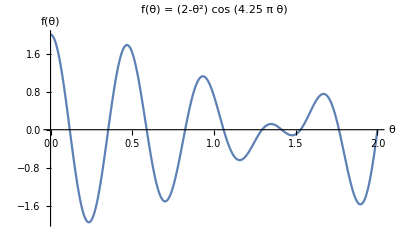

```mathematica
Plot[

(* Function(s) to plot go first. *)
Cos[4.25θ π] (2-θ^2) ,

(* The x-axis variable and its range go second. *)
{θ,0,2},

(* Presentation options go last. *)
AxesLabel->{"θ", "f(θ)"}, 
PlotLabel->"f(θ) = (2-θ^2) cos (4.25 π θ)"
]
```

• One can make this look a fair bit nicer by using better axes fonts throughout, set using the LabelStyle option.
• Adding grid lines is also very easy and automated: GridLines→Automatic.
• Similarly adding a frame is another easy improvement: Frame→True.
• Lastly, we can use different line styles and vibrant colours with e.g.: PlotStyle→{Red,Dashed,Thick}

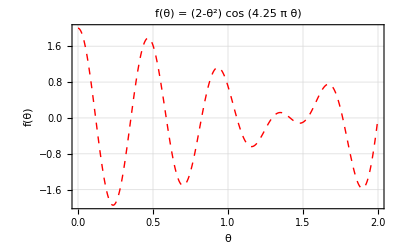

```mathematica
Plot[

(* Function(s) to plot go first. *)
Cos[4.25θ π] (2-θ^2) ,

(* The x-axis variable and its range go second. *)
{θ,0,2},

(* Presentation options go last. *)
AxesLabel->{"θ", "f(θ)"}, 
PlotLabel->"f(θ) = (2-θ^2) cos (4.25 π θ)",

(* Make the fonts look better throughout *)
LabelStyle->{Black,FontSize->14},

(* Frame the plot *)
Frame->True,

(* Gridlines *)
GridLines->Automatic,

(* Nice thick dashed line *)
PlotStyle->{Red,Thick,Dashed}
]
```

### If you make it this far, please take some time to try a few problems of your own.

K. Hamilton
Based on J. Bhamrah, A.H. Harker
Last revision 14:20 09 Jan 2023